```mathematica
Clear["Global`*"];
```

### Plot settings

```mathematica
Import[NotebookDirectory[] <>"/tools/LogScale.m"];
Import[NotebookDirectory[] <>"/tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ticksx=LogTicks[-15, -2,2];
ticksy=LogTicks[0,2,1];
ticksx0=LogTicksNoLabel[-14,-2];
ticksy0=LogTicksNoLabel[0,2];
ticksy=Join[ {{0.,"1"},{1.,"10"},{2.,"100"}},LogTicksNoLabel[0,2]];
```

```mathematica
barlegend=BarLegend[{Blend[{{0,Hue[0.,0.1,1]},{1,Hue[0.,1,1]},{1.01,Hue[0.3,0.1,1]},{2,Hue[0.3,1,1]},{2.01,Hue[0.7,0.1,1]},{3,Hue[0.7,1,1]}},#]&,{0,3}},"Ticks"->{0,1,2,3},"TickLabels"->{"0.1","1","10","100"},LegendLabel->Style[HoldForm["ϵ_S"],20,Black,FontFamily->"Times"],LabelStyle->{FontFamily->"Times",FontSize->20},LegendLayout->"Column",ColorFunctionScaling->False];
```

### Experimental sensitivities

#### KATRIN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
KATRINdata=Import[NotebookDirectory[]<>"/exp_sensitivity/KATRINXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
KATRINres= Table[{KATRINdata⟦i,1⟧,KATRINdata⟦i,2⟧*4} ,{i,1,Length[KATRINdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
KATRINtr=Transpose[{Table[KATRINres⟦i,2⟧,{i,1,Length[KATRINres]}],Table[KATRINres⟦i,1⟧,{i,1,Length[KATRINres]}]}];
```

```mathematica
KATRIN= Join[{{10^3,First[KATRINtr]⟦2⟧}},KATRINtr,{{10^3,Last[KATRINtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
KATLog = Table[{Log10[KATRIN⟦i,1⟧], Log10[KATRIN⟦i,2⟧]}, {i ,1,Length[KATRIN]}];
```

#### TRISTAN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANres= Table[{TRISTANdata⟦i,1⟧,TRISTANdata⟦i,2⟧*4} ,{i,1,Length[TRISTANdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANtr=Transpose[{Table[TRISTANres⟦i,2⟧,{i,1,Length[TRISTANres]}],Table[TRISTANres⟦i,1⟧,{i,1,Length[TRISTANres]}]}];
```

```mathematica
TRISTAN= Join[{{10^3,First[TRISTANtr]⟦2⟧}},TRISTANtr,{{10^3,Last[TRISTANtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRILog = Table[{Log10[TRISTAN⟦i,1⟧], Log10[TRISTAN⟦i,2⟧]}, {i ,1,Length[TRISTAN]}];
```

#### TRISTAN statistical

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANstatdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANstatXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANstatres= Table[{TRISTANstatdata⟦i,1⟧,TRISTANstatdata⟦i,2⟧*4} ,{i,1,Length[TRISTANstatdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANstattr=Transpose[{Table[TRISTANstatres⟦i,2⟧,{i,1,Length[TRISTANstatres]}],Table[TRISTANstatres⟦i,1⟧,{i,1,Length[TRISTANstatres]}]}];
```

```mathematica
TRISTANstat= Join[{{10^3,First[TRISTANstattr]⟦2⟧}},TRISTANstattr,{{10^3,Last[TRISTANstattr]⟦2⟧}}];
```

```mathematica
ListLogLogPlot[{KATRIN, TRISTAN, TRISTANstat}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRIstatLog = Table[{Log10[TRISTANstat⟦i,1⟧], Log10[TRISTANstat⟦i,2⟧]}, {i ,1,Length[TRISTANstat]}];
```

#### ECHo

taken from "A White Paper on keV Sterile Neutrino Dark Matter" [arXiv:1602.04816v1]
x-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4
y-axis:  m_s , non-log scale, [GeV]

```mathematica
ECHodata=Import[NotebookDirectory[]<>"/exp_sensitivity/ECHoYaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
ECHores= Table[{ECHodata⟦i,1⟧*4,ECHodata⟦i,2⟧} ,{i,1,Length[ECHodata]}];
```

```mathematica
(*the data are now in the plane (sin^2(2θ), Subscript[m, s])*)
```

```mathematica
ECHo= Join[{{10^3,First[ECHores]⟦2⟧}},ECHores,{{10^3,Last[ECHores]⟦2⟧}}];
```

```mathematica
(*rescale to bring the data in keV instead of GeV*)
ECHor = Table[{ECHo⟦i,1⟧,ECHo⟦i,2⟧*10^6} ,{i,1,Length[ECHo]}];
```

```mathematica
ListLogLogPlot[ECHor];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
ECHoLog =  Table[{Log10[ECHor⟦i,1⟧], Log10[ECHor⟦i,2⟧]}, {i ,1,Length[ECHor]}];
```

#### HUNTER phase 1

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER1data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp1XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER1res= Table[{HUNTER1data⟦i,1⟧,HUNTER1data⟦i,2⟧*4} ,{i,1,Length[HUNTER1data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER1tr=Transpose[{Table[HUNTER1res⟦i,2⟧,{i,1,Length[HUNTER1res]}],Table[HUNTER1res⟦i,1⟧,{i,1,Length[HUNTER1res]}]}];
```

```mathematica
HUNTER1= Join[{{10^3,First[HUNTER1tr]⟦2⟧}},HUNTER1tr,{{10^3,Last[HUNTER1tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER1r = Table[{HUNTER1⟦i,1⟧,HUNTER1⟦i,2⟧*10^6} ,{i,1,Length[HUNTER1]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT1Log = Table[{Log10[HUNTER1r⟦i,1⟧], Log10[HUNTER1r⟦i,2⟧]}, {i ,1,Length[HUNTER1r]}];
```

#### HUNTER phase 2

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER2data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp2XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER2res= Table[{HUNTER2data⟦i,1⟧,HUNTER2data⟦i,2⟧*4} ,{i,1,Length[HUNTER2data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER2tr=Transpose[{Table[HUNTER2res⟦i,2⟧,{i,1,Length[HUNTER2res]}],Table[HUNTER2res⟦i,1⟧,{i,1,Length[HUNTER2res]}]}];
```

```mathematica
HUNTER2= Join[{{10^3,First[HUNTER2tr]⟦2⟧}},HUNTER2tr,{{10^3,Last[HUNTER2tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER2r = Table[{HUNTER2⟦i,1⟧,HUNTER2⟦i,2⟧*10^6} ,{i,1,Length[HUNTER2]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT2Log = Table[{Log10[HUNTER2r⟦i,1⟧], Log10[HUNTER2r⟦i,2⟧]}, {i ,1,Length[HUNTER2r]}];
```

#### HUNTER phase 3

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER3data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp3XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER3res= Table[{HUNTER3data⟦i,1⟧,HUNTER3data⟦i,2⟧*4} ,{i,1,Length[HUNTER3data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER3tr=Transpose[{Table[HUNTER3res⟦i,2⟧,{i,1,Length[HUNTER3res]}],Table[HUNTER3res⟦i,1⟧,{i,1,Length[HUNTER3res]}]}];
```

```mathematica
HUNTER3= Join[{{10^3,First[HUNTER3tr]⟦2⟧}},HUNTER3tr,{{10^3,Last[HUNTER3tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)HUNTER3r = Table[{HUNTER3⟦i,1⟧,HUNTER3⟦i,2⟧*10^6} ,{i,1,Length[HUNTER3]}];
```

```mathematica
ListLogLogPlot[{HUNTER1r, HUNTER2r, HUNTER3r}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT3Log = Table[{Log10[HUNTER3r⟦i,1⟧], Log10[HUNTER3r⟦i,2⟧]}, {i ,1,Length[HUNTER3r]}];
```

#### DM lifetime constraint

This line derives from the requirement that sterile neutrino dark matter (whose main decay channel is into 3 active neutrinos) is stable on timescale comparable to the age of the universe. More on that can be found in 
[1602.04816v2] in “2.4.2 keV-scale”
[hep-ph/0009083], in section “3. Decay”
[astro-ph/0101524], in section “IX. COSMOLOGICAL CONSTRAINTS ON STERILE NEUTRINOS”.

```mathematica
mainchannelbound={10^#,(267/10^#)^(1/5)}&/@Table[i,{i,-14,-1,0.1}];
mainchannelbound= Table[{mainchannelbound[[i,1]],mainchannelbound[[i,2]]} ,{i,1,Length[mainchannelbound]}];
mainchannelbound= Join[{{10^3,First[mainchannelbound][[2]]}},mainchannelbound,{{10^3,Last[mainchannelbound][[2]]}}];
mainchannelboundLog =  Table[{Log10[mainchannelbound[[i,1]]], Log10[mainchannelbound[[i,2]]]}, {i ,1,Length[mainchannelbound]}];
```

#### X-rays bound - new

Data relative to the constraint coming from X-ray observations, newly digitized from 1311.0282 , 1609.00667, and 1901.01262, and combined to cover the range of  sterile neutrino masses (1 keV - 100 keV) and be the most stringent ones. 
They are in the shape  {{m_s, sin^2(2θ)}}, ordered for increasing m_s in keV.

```mathematica
Xdatanew= Import[NotebookDirectory[]<>"/data/most_stringent_Xray_Xsortincr.dat" ];
Xdatanew=Join[{{1.373,9.54192511100296*^-1}}, Xdatanew];
Xdatanew= Join[{{10^3,First[Xdatanew]⟦2⟧}},Xdatanew,{{10^3,Last[Xdatanew]⟦2⟧}}];
(*we put them in the shape {{sin^2(2θ), Subscript[m, s]}}*)
Xdatanewtr=Table[{Xdatanew⟦i,2⟧,Xdatanew⟦i,1⟧} ,{i,1,Length[Xdatanew]}];
(*take the Log10 to plot them more easily*)
XnewLog= Table[{Log10[Xdatanewtr⟦i,1⟧], Log10[Xdatanewtr⟦i,2⟧]}, {i ,1,Length[Xdatanewtr]}];
```

X-ray bound reduced - Cocktail DM

```mathematica
Xnewred10=  Table[{Xdatanewtr⟦i,1⟧*10,Xdatanewtr⟦i,2⟧} ,{i,1,Length[Xdatanewtr]}];
Xnewred100=  Table[{Xdatanewtr⟦i,1⟧*100,Xdatanewtr⟦i,2⟧} ,{i,1,Length[Xdatanewtr]}];
```

```mathematica
(*take the Log10 to plot them more easily*)
Xnewred10Log = Table[{Log10[Xnewred10⟦i,1⟧], Log10[Xnewred10⟦i,2⟧]}, {i ,1,Length[Xnewred10]}];
Xnewred100Log = Table[{Log10[Xnewred100⟦i,1⟧], Log10[Xnewred100⟦i,2⟧]}, {i ,1,Length[Xnewred100]}];
```

#### Lines for plot

experimental sensitivities for 100% DM fraction

```mathematica
expsensitivity012 = {
Purple, Thick,Thickness[0.005],Line[XnewLog],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Lighter[Brown], Thick,Thickness[0.005],Line[HUNT1Log],
Lighter[Brown], DotDashed,Thickness[0.005],Line[HUNT2Log],
Lighter[Brown], Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],DotDashed,Thickness[0.005], Line[KATLog],
Lighter[Blue],Dashed,Thickness[0.005],Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]};
```

```mathematica
epilogue012 = {
FontSize->17,
Purple, Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.12", Bold],-0 Degree],Scaled[{0.12,0.36}]], 
FontSize->14,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-74 Degree],Scaled[{0.585,0.3}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-74 Degree],Scaled[{0.67,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-74 Degree],Scaled[{0.895,0.34}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.88,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.72,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.41,0.85}]],
Lighter[Blue], Text[Rotate[Style["ECHo\n sensitivity", Bold],-0 Degree],Scaled[{0.815,0.22}]]
};
```

experimental sensitivities for 10% DM fraction

```mathematica
expsensitivity0012 = {
Lighter[Purple], Thick,Thickness[0.005],Line[Xnewred10Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Lighter[Brown], Thick,Thickness[0.005],Line[HUNT1Log],
Lighter[Brown], DotDashed,Thickness[0.005],Line[HUNT2Log],
Lighter[Brown], Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.004],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],DotDashed,Thickness[0.005], Line[KATLog],
Lighter[Blue],Dashed,Thickness[0.005],Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]};
```

```mathematica
epilogue0012 = {
FontSize->14,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-74 Degree],Scaled[{0.585,0.3}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-74 Degree],Scaled[{0.67,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-74 Degree],Scaled[{0.895,0.34}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.88,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.72,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.41,0.85}]],
Lighter[Blue], Text[Rotate[Style["ECHo\n sensitivity", Bold],-0 Degree],Scaled[{0.815,0.22}]]
};
```

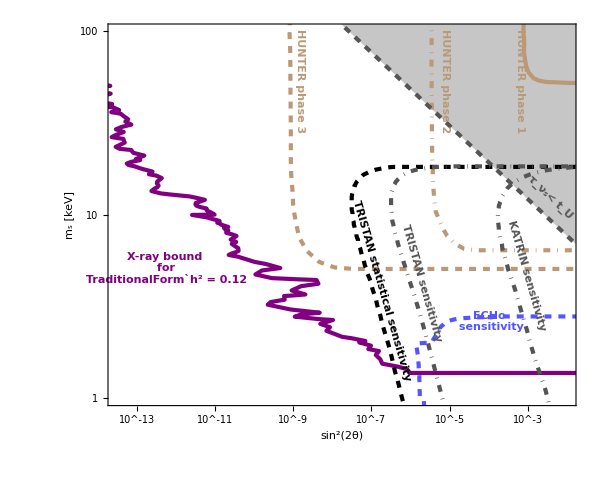

```mathematica
Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times New Roman"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,(* PlotLabel->Row[{
"Experimental sensitivities"}],*)
Prolog->expsensitivity012,
Epilog->epilogue012,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Dataset for plots

#### get relic abundance lines with 100 % DM fraction

```mathematica
getabundance100 = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["omegadm_scalar_``_``.dat",vals];
omegadm100[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/abundance012/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
epsilon = Join[Table[i,{i,0.1,0.9,0.1}],Table[i,{i,1,9,1}],Table[i,{i,10,100,1}]];
getabundance100[10,0];
getabundance100[10,#]&/@ epsilon;
getabundance100[50,#]&/@ epsilon;
getabundance100[100,#]&/@ epsilon;
```

#### get relic abundance lines with 10% DM fraction

```mathematica
getabundance10 = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["omegadm_scalar_``_``.dat",vals];
omegadm10[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/abundance0012/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
getabundance10[10,0];
```

```mathematica
getabundance10[10,#]&/@ epsilon;
getabundance10[50,#]&/@ epsilon;
getabundance10[100,#]&/@ epsilon;
```

### Parameter space for m_ϕ = 10GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[10,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm100[10,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[10,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

```mathematica
epilogue10 = Join[epilogue012,
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + scalar NSSI\n m_ϕ = 10 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.17,0.1}]]}];parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_10_012.pdf",parameterspace];
```

### Parameter space for m_ϕ = 50GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[50,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm100[50,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[50,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

```mathematica
epilogue10 = Join[epilogue012,
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + scalar NSSI\n m_ϕ = 50 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.17,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_50_012.pdf",parameterspace];
```

### Parameter space for m_ϕ = 100GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[100,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.007],Line[omegadm100[100,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[100,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

```mathematica
epilogue10 = Join[epilogue012,
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + scalar NSSI\n m_ϕ = 100 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.17,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_100_012.pdf",parameterspace];
```

### Parameter space for m_ϕ = 10GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[10,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.0065],Line[omegadm10[10,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm10[10,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,
{FontSize->15,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.1,0.45}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 10 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_10_0012.pdf",parameterspace];
```

### Parameter space for m_ϕ = 50GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[50,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm10[50,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.006],Line[omegadm10[50,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,
{FontSize->13,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.525,0.09}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 50 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_50_0012.pdf",parameterspace];
```

### Parameter space for m_ϕ = 100GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[100,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.0065],Line[omegadm10[100,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.006],Line[omegadm10[100,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,
{FontSize->13,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.525,0.09}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 100 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]];
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_scalar_100_0012.pdf",parameterspace];
```